```mathematica
$Assumptions = {{r1111[t],r1010[t],r0101[t],r0000[t]}∈Reals, {r1110[t],r1101[t],r1100[t],r1001[t],r1000[t],r0100[t]}∈Complexes, 
{c1110[t],c1101[t],c1100[t],c1001[t], c1000[t], c0100[t]}∈Complexes};
```

Defining some constants/variables/parameters:

```mathematica
ℏ:=1;
Ω=1.5;
Δ=0.2;
Vij=0.5;
ΓA=-0.1;
ΓB=-0.1;
```

Defining the 4x4 density matrix of the two partitions (2 ensembles):

```mathematica
rhoM[t_] :=({{r1111[t], r1110[t], r1101[t], r1100[t]}, {c1110[t], r1010[t], r1001[t], r1000[t]}, {c1101[t], c1001[t], r0101[t], r0100[t]}, {c1100[t], c1000[t], c0100[t], r0000[t]}});
```

Defining the  density matrix at t=0:

```mathematica
rhoM0 :=({{0, 0, 0, 0}, {0, 1.0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

Defining the basis set for single-partition:

```mathematica
g:=({{1}, {0}});e:=({{0}, {1}});
```

Defining the ladder operators in terms of a single-partition basis:

```mathematica
sigmage:=KroneckerProduct[g,Transpose[e]];
sigmaeg:=KroneckerProduct[e,Transpose[g]];
sigmaee:=KroneckerProduct[e,Transpose[e]];
```

Defining the Hamiltonian:

```mathematica
Hamiltonian := ({{2Ω, 0, 0, -Vij/2}, {0, -Δ, -Vij/2, 0}, {0, -Vij/2, Δ, 0}, {-Vij/2, 0, 0, -2Ω}})
```

Defining the Liouvillian due to Spontaneous Emission:

```mathematica
Gspon :=({{-(ΓA+ΓB), -ΓA/2, -ΓB/2, -(ΓA+ΓB)/2}, {0, ΓA-ΓB, -ΓA/2, -ΓA/2}, {0, -ΓB/2, ΓA-ΓB, -ΓB/2}, {-(ΓA+ΓB)/2, 0, 0, 2(ΓA+ΓB)}});
```

Defining the Liouvillian due to De-phasing:

```mathematica
Gdephase :=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

Defining the Liouvillian due to Thermal fluctuations:

```mathematica
Gtherm :=({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

Defining the RHS of the Master Equation (von Neumann eq.):

```mathematica
RHS:=Refine[ⅈ/ℏ*(Hamiltonian.rhoM[t]-rhoM[t].Hamiltonian)];
```

Defining the Homogenous Master Equation:

```mathematica
root:=Refine[rhoM'[t]-RHS+Gspon+Gtherm+Gdephase];
```

Defining the equations for each element of the density matrix (Only 10 are important due to the fact that Rho_ij = Rho_ji*):

```mathematica
eq1:=root[[1,1]]==0;
eq2:=root[[1,2]]==0;
eq3:=root[[1,3]]==0;
eq4:=root[[1,4]]==0;
eq5:=root[[2,1]]==0;
eq6:=root[[2,2]]==0;
eq7:=root[[2,3]]==0;
eq8:=root[[2,4]]==0;
eq9:=root[[3,1]]==0;
eq10:=root[[3,2]]==0;
eq11:=root[[3,3]]==0;
eq12:=root[[3,4]]==0;
eq13:=root[[4,1]]==0;
eq14:=root[[4,2]]==0;
eq15:=root[[4,3]]==0;
eq16:=root[[4,4]]==0;
```

Showing the significant equations:

```mathematica
eq1(*r1111*)
```

0.2-ⅈ (0.-0.25 c1100[t]+0.25 r1100[t])+r1111'[t]==0

```mathematica
eq2(*r1110*)
```

0.05-ⅈ (-0.25 c1000[t]+0.25 r1101[t]+3.2 r1110[t])+r1110'[t]==0

```mathematica
eq3(*r1101*)
```

0.05-ⅈ (-0.25 c0100[t]+2.8 r1101[t]+0.25 r1110[t])+r1101'[t]==0

```mathematica
eq4(*r1100*)
```

0.1-ⅈ (-0.25 r0000[t]+6. r1100[t]+0.25 r1111[t])+r1100'[t]==0

```mathematica
eq6(*r1010*)
```

0.-ⅈ (0.-0.25 c1001[t]+0.25 r1001[t])+r1010'[t]==0

```mathematica
eq7(*r1001*)
```

0.05-ⅈ (-0.25 r0101[t]-0.4 r1001[t]+0.25 r1010[t])+r1001'[t]==0

```mathematica
eq8(*r1000*)
```

0.05-ⅈ (0.25 c1110[t]-0.25 r0100[t]+2.8 r1000[t])+r1000'[t]==0

```mathematica
eq11(*r0101*)
```

0.-ⅈ (0.+0.25 c1001[t]-0.25 r1001[t])+r0101'[t]==0

```mathematica
eq12(*r0100*)
```

0.05-ⅈ (0.25 c1101[t]+3.2 r0100[t]-0.25 r1000[t])+r0100'[t]==0

```mathematica
eq16(*r0000*)
```

-0.4-ⅈ (0.+0.25 c1100[t]-0.25 r1100[t])+r0000'[t]==0

Solving the equations with de DSolve[] method:

```mathematica
sol=NDSolve[{eq1, eq2,eq3,eq4,eq5,eq6,eq7,eq8,eq9, eq10,eq11,eq12,eq13, eq14, eq15, eq16, r1111[0]==0,r1110[0]==0,r1101[0]==0,r1100[0]==0,r1010[0]==1,r1001[0]==0,r1000[0]==0,r0101[0]==0,r0100[0]==0,r0000[0]==0, c1110[0]==0,c1101[0]==0,c1100[0]==0,c1001[0]==0, c1000[0]==0, c0100[0]==0},{r1111[t],r1110[t],r1101[t],r1100[t],r1010[t],r1001[t],r1000[t],r0101[t],r0100[t],r0000[t], c1110[t],c1101[t],c1100[t],c1001[t], c1000[t], c0100[t]},{t , 0,100}];
```

```mathematica
sol
```

{{r1111[t]→InterpolatingFunction[…][t],r1110[t]→InterpolatingFunction[…][t],r1101[t]→InterpolatingFunction[…][t],r1100[t]→InterpolatingFunction[…][t],r1010[t]→InterpolatingFunction[…][t],r1001[t]→InterpolatingFunction[…][t],r1000[t]→InterpolatingFunction[…][t],r0101[t]→InterpolatingFunction[…][t],r0100[t]→InterpolatingFunction[…][t],r0000[t]→InterpolatingFunction[…][t],c1110[t]→InterpolatingFunction[…][t],c1101[t]→InterpolatingFunction[…][t],c1100[t]→InterpolatingFunction[…][t],c1001[t]→InterpolatingFunction[…][t],c1000[t]→InterpolatingFunction[…][t],c0100[t]→InterpolatingFunction[…][t]}}

Extracting solutions of the significant equations:

```mathematica
sol1= r1111[t]/.sol[[1,1]];
sol2= r1110[t]/.sol[[1,2]];
sol3= r1101[t]/.sol[[1,3]];
sol4= r1100[t]/.sol[[1,4]];
sol5= r1010[t]/.sol[[1,5]];
sol6= r1001[t]/.sol[[1,6]];
sol7= r1000[t]/.sol[[1,7]];
sol8= r0101[t]/.sol[[1,8]];
sol9= r0100[t]/.sol[[1,9]];
sol10= r0000[t]/.sol[[1,10]];
sol11 = c1110[t]/.sol[[1,11]];
sol12 =c1101[t]/.sol[[1,12]];
sol13 = c1100[t]/.sol[[1,13]];
sol14 = c1001[t]/.sol[[1,14]];
sol15 =  c1000[t]/.sol[[1,15]];
sol16 =  c0100[t]/.sol[[1,16]];
```

Plots of solutions of the significant equations:

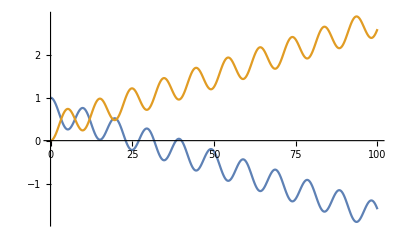

```mathematica
Plot[{Re[sol5], Re[sol8]}, {t, 0,100}, PlotRange->All]
```

```mathematica
(*Plot[Re[sol1], {t, 0,10}]
Plot[{Re[sol2], Re[sol11]}, {t, 0,10}]
Plot[{Re[sol3], Re[sol12]}, {t, 0,10}]
Plot[{Re[sol4], Re[sol13]}, {t, 0,10}]
Plot[Re[sol5], {t,0, 10}]
Plot[{Re[sol6], Re[sol14]}, {t, 0,10}]
Plot[{Re[sol7], Re[sol15]}, {t, 0,10}]
Plot[Re[sol8], {t, 0,10}]
Plot[{Re[sol9], Re[sol16]}, {t, 0,10}]
Plot[Re[sol10], {t,0,10}]*)
```